# Testing the ‘Rosetta Stone’ approach to derive the coefficients in the firing rate equation from Residues

## Written by Maurizio Mattia, July 2022, Rome - Italy

## Script plotting the panels in Figs. 2-3 of (Vinci & Mattia, 2024)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["LIFLibrary.m",Path-> NotebookDirectory[]]
```

```mathematica
Needs["NumericalCalculus`"]
```

## Neuron parameters used in this notebook

Membrane potential decay time in seconds:

```mathematica
τ=0.020;
```

Emission threshold in mV:

```mathematica
Vt=20.;
```

Reset potential in mV (0 is the resting potential):

```mathematica
Vr=0.;
```

Absolute refractory period in seconds:

```mathematica
Tarp=0.;
```

Note that in what follows both the mean (μ) and standard deviation (σ) of the input current are expressed in mV, meaning that actually they are respectively μ τ and σ √τ.

This is the current-to-rate gain function. To have it in Hz it must be divided by τ.

```mathematica
Φ[Xr_,Xt_]:=1/MFPT[Xr,Xt];
```

### Guesses for the eigenvalues λ_n at μτ=(v_thr + v_res)/2

The theoretical guesses from Eq. (13.9.10) in DLMF 2010. This is valid for large (n^2 π^2)/(2 Xt^2).

```mathematica
LambdasAtBifurcationLargeN[Xt_,NumOfLambdas_]:=
Table[(-3 n^2 π^2+3 Xt^2-Xt^4)/(6 Xt^2),{n,NumOfLambdas}];
```

```mathematica
LambdasAtBifurcation[Xt_,λτRange_]:=Module[{λτ,n},
λτ=2Range[Quotient[Min[λτRange],2],Quotient[Max[λτRange],2]];
λτ=If[λτ[[1]]<Min[λτRange],Take[λτ,1-Length[λτ]],λτ];
For[n=1,Min[λτRange]<(-3 n^2 π^2+3 Xt^2-Xt^4)/(6 Xt^2),n++,AppendTo[λτ,(-3 n^2 π^2+3 Xt^2-Xt^4)/(6 Xt^2)]];
Sort[λτ,Greater]
]
```

```mathematica
LambdasBeyondBifurcation[Xr_,Xt_,λτRange_]:=Module[{λτ,λτ0,z,ExitFor,PhiTau,n},
PhiTau=Φ[Xr,Xt];
ExitFor=False;
λτ={};
For[n=1,Not[ExitFor],n++,
λτ0=-(2 π^2 n^2)/(Xt-Xr)^2+ⅈ 2π PhiTau  n;
If[Re[λτ0]<=Max[λτRange],
If[Re[λτ0]>=Min[λτRange],AppendTo[λτ,λτ0],ExitFor=True],Null]
];
λτ=GetLambdasFromGuess[Xr,Xt,λτ];
λτ=Flatten[Append[λτ,Conjugate[λτ]]];
λτ=Flatten[Append[λτ,z/.NSolve[CERS[z,Xr,Xt]==0 && Min[λτRange]<z<Max[λτRange],z,Reals]]];
Sort[λτ,Re[#1]>Re[#2]&]
]
```

Revised expression of the non-normalized (NN) eigenfunctions ψ(x,λ) referring to (Ricciardi & Sato, 1988) [RS88] and the related characteristic equation for the eigenvalues:

```mathematica
(* This is the same as the following Initialization cell but can be used to define the characteristic equation as in (Mattia & Del Giudice 2002). This is why here the eigenfunctions ψ are multiplied by Gamma[λ/2]. *)ψNN[x_,λ_]=Gamma[λ/2]/Gamma[(λ+1)/2] Hypergeometric1F1[λ/2,1/2,x^2]+2x Hypergeometric1F1[(1+λ)/2,3/2,x^2];
CERS[λ_,Xr_,Xt_]=ψNN[Xt,λ]-ψNN[Xr,λ];
```

```mathematica
ψNN[x_,λ_]=Hypergeometric1F1[λ/2,1/2,x^2]/Gamma[(λ+1)/2]+2x Hypergeometric1F1[(1+λ)/2,3/2,x^2]/Gamma[λ/2];
ρISI[s_,Xr_,Xt_]=ψNN[Xr,s]/ψNN[Xt,s];
CERS[λ_,Xr_,Xt_]=ρISI[λ,Xr,Xt]-1;
```

```mathematica
h[s_,Xr_,Xt_]=ρISI[s,Xr,Xt]/(1-ρISI[s,Xr,Xt]);
```

```mathematica
Series[ψNN[x,λ],{λ,0,1}]
```

1/(√π)+((π Erfi[x]-PolyGamma[0,1/2]+Hypergeometric1F1^(1,0,0)[0,1/2,x^2]) λ)/(2 √π)+O[λ]^2

### Supra - threshold example network of LIF neurons for the Figures of (Vinci & Mattia, 2024)

```mathematica
(* σ2τ=4.754537201220373^2; *)
σ2τ=4.5^2;
```

As workbench we compute the eigenvalues of the FP operator just before the so-called bifurcation value for the mean synaptic current:  μτ=(Vt+Vr)/2. This choice allows us to be sure that all λ_n are nonpositive reals:

```mathematica
Module[{μτ=Vt-3, λτRange={-275,-0.1},n},
XtTest=(Vt-μτ)/(√σ2τ);XrTest=(Vr-μτ)/(√σ2τ);

Nu0=Φ[XrTest,XtTest];
Print["Φ[Xr,Xt] = ",Nu0];
Print["Φ[Xr,Xt]/τ = ",Nu0/τ," Hz"];

λτTest=LambdasBeyondBifurcation[XrTest,XtTest,λτRange];
Print["Num. of eigenvalues = ",Length[λτTest]];
λτTest
]
```

Φ[Xr,Xt] = 0.236451

Φ[Xr,Xt]/τ = 11.8225 Hz

Num. of eigenvalues = 118

{-1.44824-1.91068 ⅈ,-1.44824+1.91068 ⅈ,-4.59833-4.37306 ⅈ,-4.59833+4.37306 ⅈ,-9.4864-6.70067 ⅈ,-9.4864+6.70067 ⅈ,-11.4891,-15.5349,-16.4096-8.90194 ⅈ,-16.4096+8.90194 ⅈ,-22.3824,-25.3687-11.0895 ⅈ,-25.3687+11.0895 ⅈ,-25.5234,-28.5551,-31.501,-34.3806,-36.3419-13.2771 ⅈ,-36.3419+13.2771 ⅈ,-37.2079,-42.7334,-45.4425,-48.1233,-49.3212-15.4666 ⅈ,-49.3212+15.4666 ⅈ,-53.4121,-58.6147,-61.1895,-63.7492,-64.3031-17.6578 ⅈ,-64.3031+17.6578 ⅈ,-66.2948,-68.8267,-71.3454,-76.3476,-78.8335,-81.2859-19.8504 ⅈ,-81.2859+19.8504 ⅈ,-81.3103,-83.7782,-86.2373,-88.6878,-91.1302,-93.5652,-98.4155,-100.269-22.0442 ⅈ,-100.269+22.0442 ⅈ,-100.832,-103.242,-105.646,-110.436,-112.823,-115.206,-117.583,-121.251-24.2388 ⅈ,-121.251+24.2388 ⅈ,-124.691,-129.409,-131.761,-134.11,-136.455,-138.796,-141.135,-143.47,-144.233-26.4341 ⅈ,-144.233+26.4341 ⅈ,-148.132,-150.458,-152.781,-155.1,-159.731,-164.352,-166.659,-169.214-28.6299 ⅈ,-169.214+28.6299 ⅈ,-171.265,-173.565,-175.863,-178.158,-180.45,-182.74,-187.315,-189.599,-191.881,-194.162,-196.194-30.8262 ⅈ,-196.194+30.8262 ⅈ,-196.441,-198.718,-203.267,-205.538,-207.808,-212.342,-214.606,-216.869,-219.131,-221.391,-223.65,-225.172-33.0228 ⅈ,-225.172+33.0228 ⅈ,-225.907,-228.163,-230.418,-232.671,-237.172,-239.42,-246.158,-248.401,-250.644,-252.885,-255.125,-256.149-35.2197 ⅈ,-256.149+35.2197 ⅈ,-259.602,-261.838,-266.308,-268.541,-270.773}

Here we select only the first 100 eigenvalues/eigenmodes out of the 118 found. The last two eigenvalues are complex conjugates.

```mathematica
Table[{n,λτTest[[n]]},{n,99,101}]
```

{{99,-225.172-33.0228 ⅈ},{100,-225.172+33.0228 ⅈ},{101,-225.907}}

```mathematica
λτTest=Take[λτTest,100];
```

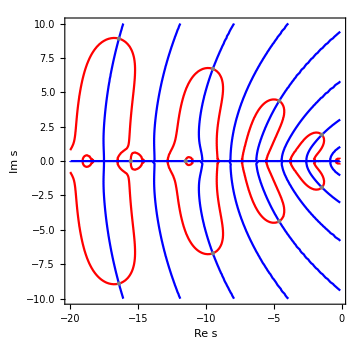

```mathematica
Module[{μτ=Vt-3, ReλτRange={-20,-0.1}, ImλτRange={-10,10},λτ0},
XtTest=(Vt-μτ)/(√σ2τ);XrTest=(Vr-μτ)/(√σ2τ);
hgCE=Show[ContourPlot[{Re[CERS[x+ⅈ y,XrTest,XtTest]]==0,Im[CERS[x+ⅈ y,XrTest,XtTest]]==0} ,{x,Min[ReλτRange],Max[ReλτRange]},{y,Min[ImλτRange],Max[ImλτRange]},ContourStyle->{Red,Blue},FrameLabel->{"Re s","Im s"}],ListPlot[Table[{Re[λτTest[[n]]],Im[λτTest[[n]]]},{n,Length[λτTest]}],PlotStyle->Directive[Gray,PointSize[Large]]],ImageSize->360]
]
```

```mathematica
Export["CEcontourplot.pdf",hgCE]
```

CEcontourplot.pdf

These are the computed eigenvalues:

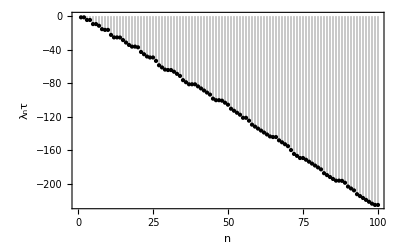

```mathematica
ListPlot[Re[λτTest],Filling->Axis,Filling->LightGray,PlotStyle->Directive[Black,PointSize[Medium]],FrameLabel->{"n","λ_nτ"},Frame->True]
```

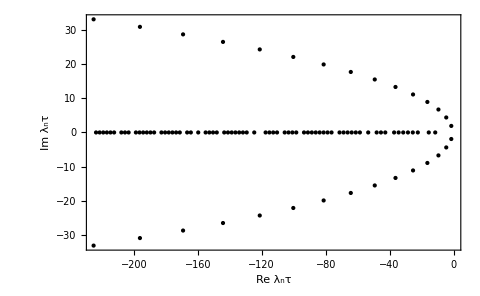

```mathematica
hEV=ListPlot[Table[{Re[λτTest[[n]]],Im[λτTest[[n]]]},{n,Length[λτTest]}],PlotStyle->Directive[Black,PointSize[Medium]],FrameLabel->{"Re λ_nτ","Im λ_nτ"},Frame->True,ImageSize->480]
```

```mathematica
Export["Eigenvalues.pdf",hEV]
```

Eigenvalues.pdf

```mathematica
ExpandFileName["Eigenvalues.pdf"]
```

C:\Users\Mattia\Documents\Eigenvalues.pdf

From the eigenvalues the non-normalized eigenfunctions ψ_n(v_res) are

```mathematica
Table[ψNN[XrTest,λτTest[[n]]],{n,Length[λτTest]}]
```

{-3.22778+2.51339 ⅈ,-3.22778-2.51339 ⅈ,128.894-273.704 ⅈ,128.894+273.704 ⅈ,224294.+1737.76 ⅈ,224294.-1737.76 ⅈ,-56.4814,-3444.13,9.43843×10^8-4.21002×10^9 ⅈ,9.43843×10^8+4.21002×10^9 ⅈ,-2.86675×10^6,2.83638×10^15+3.77707×10^15 ⅈ,2.83638×10^15-3.77707×10^15 ⅈ,2.26591×10^8,1.81165×10^10,-1.74035×10^11,-5.80787×10^13,4.17108×10^23+2.18652×10^23 ⅈ,4.17108×10^23-2.18652×10^23 ⅈ,5.92741×10^14,-6.57279×10^18,-6.38167×10^20,5.41094×10^22,-5.7004×10^33-2.40253×10^33 ⅈ,-5.7004×10^33+2.40253×10^33 ⅈ,-3.02439×10^26,6.39468×10^29,-1.44144×10^32,7.64648×10^33,-1.18111×10^46-8.56443×10^45 ⅈ,-1.18111×10^46+8.56443×10^45 ⅈ,3.06318×10^35,-8.30507×10^37,5.94276×10^39,-5.16243×10^43,5.74565×10^45,3.43543×10^60+7.30594×10^60 ⅈ,3.43543×10^60-7.30594×10^60 ⅈ,-2.31675×10^47,-2.46741×10^49,5.49644×10^51,-4.96829×10^53,1.20544×10^55,3.67957×10^57,6.384×10^61,-4.05016×10^77+1.26369×10^78 ⅈ,-4.05016×10^77-1.26369×10^78 ⅈ,-1.74547×10^63,-5.22767×10^65,1.11116×10^68,6.0942×10^71,6.42988×10^73,-2.1034×10^76,3.02492×10^78,7.66819×10^97-2.2802×10^97 ⅈ,7.66819×10^97+2.2802×10^97 ⅈ,3.93179×10^84,1.09446×10^89,-8.16642×10^90,-2.50028×10^92,2.12278×10^95,-4.33831×10^97,5.759×10^99,-4.57202×10^101,1.3561×10^120+1.65634×10^120 ⅈ,1.3561×10^120-1.65634×10^120 ⅈ,1.31076×10^106,-2.94944×10^108,4.40941×10^110,-4.35163×10^112,8.66733×10^116,4.50869×10^121,-5.84771×10^123,1.887×10^145-2.36557×10^145 ⅈ,1.887×10^145+2.36557×10^145 ⅈ,4.1037×10^127,-2.33684×10^130,5.57299×10^132,-9.50992×10^134,1.16765×10^137,-6.36233×10^138,7.0318×10^143,-1.65509×10^146,2.90856×10^148,-3.75106×10^150,2.13757×10^173+1.57008×10^173 ⅈ,2.13757×10^173-1.57008×10^173 ⅈ,2.22725×10^152,5.65632×10^154,6.70527×10^159,-1.29175×10^162,1.90124×10^164,-1.48385×10^168,1.15992×10^171,-3.49847×10^173,7.79689×10^175,-1.37587×10^178,1.76198×10^180,1.14348×10^204-1.21953×10^204 ⅈ,1.14348×10^204+1.21953×10^204 ⅈ}

Before to continue we check that the eigenvalues solve the characteristic equation within a reasonable  numerical error (the following should be 0):

```mathematica
Max[Abs[Table[CERS[λτTest[[n]],XrTest,XtTest],{n,Length[λτTest]}]]]
```

5.00552×10^-9

Here we compute the normalized ψ_n(v_res) computed as Eq. (18) cleaning  the spurious complex values which are actually real numbers:

```mathematica
Residue[h[λτ,XrTest,XtTest],{λτ,0}]
```

0

```mathematica
Φ[XrTest,XtTest]
```

0.236451

```mathematica
ψH=Table[NResidue[h[λτ,XrTest,XtTest],{λτ,λτTest[[n]]}],{n,Length[λτTest]}];
ψH=Table[If[Abs[Im[ψH[[n]]]]<10^-10,Re[ψH[[n]]],ψH[[n]]],{n,Length[ψH]}]
```

{0.380812-0.37816 ⅈ,0.380812+0.37816 ⅈ,0.38873-0.629643 ⅈ,0.38873+0.629643 ⅈ,0.354485-0.937277 ⅈ,0.354485+0.937277 ⅈ,0.000888788,-0.00101754,0.348486-1.2648 ⅈ,0.348486+1.2648 ⅈ,-0.000353446,0.348066-1.58648 ⅈ,0.348066+1.58648 ⅈ,-0.000551973,0.000833354,0.00014525,-0.000847149,0.348314-1.9062 ⅈ,0.348314+1.9062 ⅈ,-0.000144892,0.000401061,-0.000585181,-0.000720952,0.348613-2.22514 ⅈ,0.348613+2.22514 ⅈ,0.000768557,-0.000275954,-0.000778831,-0.000503174,0.348865-2.5437 ⅈ,0.348865+2.5437 ⅈ,0.000238865,0.000748166,0.000604371,-0.000627149,-0.000738181,0.349064-2.86208 ⅈ,0.349064+2.86208 ⅈ,-0.000307792,0.000331664,0.000732437,0.00064411,0.000149358,-0.000428109,-0.00062025,0.349219-3.18035 ⅈ,0.349219+3.18035 ⅈ,-0.000150756,0.000394343,0.00071998,0.000278248,-0.000241048,-0.000637889,-0.000730876,0.349342-3.49857 ⅈ,0.349342+3.49857 ⅈ,0.00043856,0.000679646,0.000371225,-0.0000821749,-0.000498161,-0.00071772,-0.000662998,-0.000361539,0.349437-3.81674 ⅈ,0.349437+3.81674 ⅈ,0.000470897,0.00070159,0.000686803,0.000439081,-0.000355496,-0.000719805,-0.000572814,0.349516-4.13489 ⅈ,0.349516+4.13489 ⅈ,0.000146416,0.000495268,0.000694642,0.000690477,0.000489273,0.000152457,-0.000535991,-0.000701531,-0.000678979,-0.000477628,0.349581-4.45302 ⅈ,0.349581+4.45302 ⅈ,-0.00015322,0.000208275,0.000688756,0.000691997,0.000526894,-0.000107443,-0.000424149,-0.00064075,-0.000709286,-0.000616452,-0.000385554,0.349627-4.77115 ⅈ,0.349627+4.77115 ⅈ}

Eventually we plot the partial sum in Eq. (14) in (Vinci & Mattia, 2021), which should converge to Φ τ:

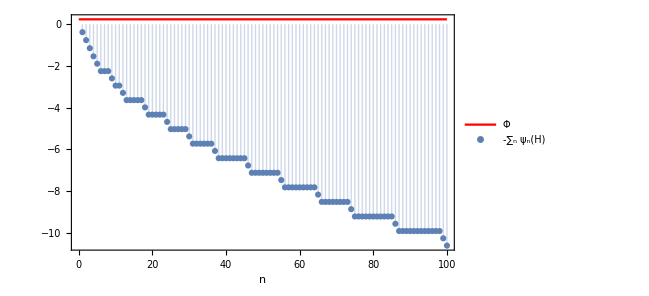

```mathematica
Show[Plot[Nu0,{x,0,Length[λτTest]},PlotStyle->Red,PlotLegends->{"Φ"}],ListPlot[-Re[Accumulate[ψH]],Filling->Axis,PlotLegends->{"-∑_n ψ_n(H)"}],Frame->True,PlotRange->All,FrameLabel->{"n",""},ImageSize->480]
```

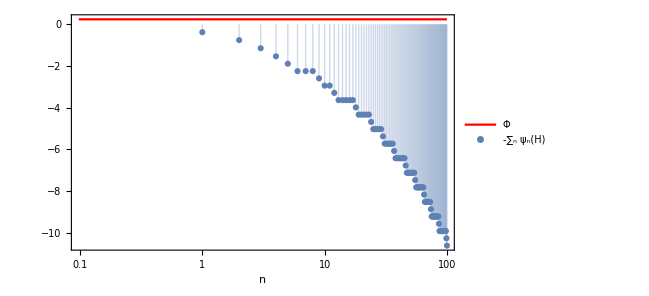

```mathematica
Show[LogLinearPlot[Nu0,{x,0,Length[λτTest]},PlotStyle->Red,PlotLegends->{"Φ"}],ListLogLinearPlot[-Re[Accumulate[ψH]],Filling->Axis,PlotLegends->{"-∑_n ψ_n(H)"}],Frame->True,PlotRange->All,FrameLabel->{"n",""},ImageSize->480]
```

```mathematica
Exp[{1,2} {3,4}]
```

{ⅇ^3,ⅇ^8}

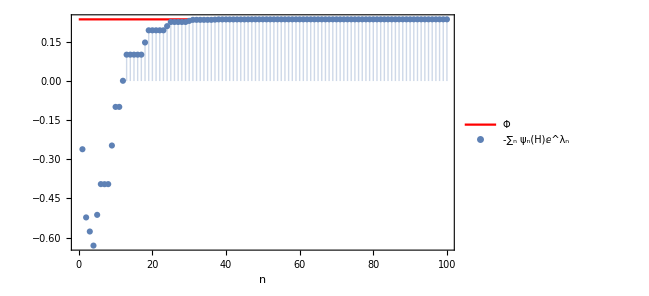

```mathematica
Δt=0.1;Show[Plot[Nu0,{x,0,Length[λτTest]},PlotStyle->Red,PlotLegends->{"Φ"}],ListPlot[-Re[Accumulate[ψH Exp[λτTest Δt]]],Filling->Axis,PlotLegends->{"-∑_n ψ_n(H)ⅇ^λ_n"}],Frame->True,PlotRange->All,FrameLabel->{"n",""},ImageSize->480]
```

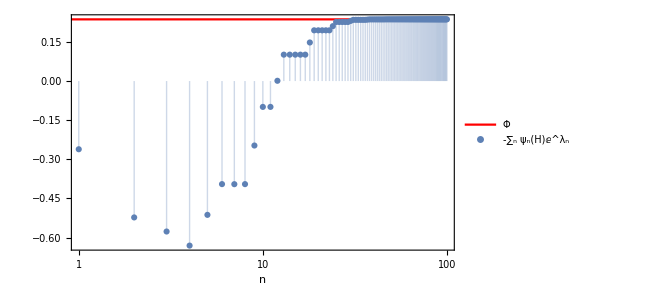

```mathematica
Δt=0.1;Show[LogLinearPlot[Nu0,{x,0,Length[λτTest]},PlotStyle->Red,PlotLegends->{"Φ"},PlotRange->{{1,Length [λτTest]},All}],ListLogLinearPlot[-Re[Accumulate[ψH Exp[λτTest Δt]]],Filling->Axis,PlotLegends->{"-∑_n ψ_n(H)ⅇ^λ_n"},PlotRange->{{1,Length [λτTest]},All}],Frame->True,FrameLabel->{"n",""},ImageSize->480]
```

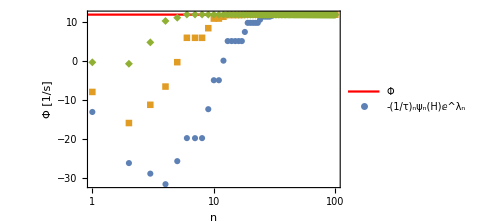

```mathematica
Δt=0.2;hgPhi=Show[LogLinearPlot[Nu0/τ,{x,0,Length[λτTest]},PlotStyle->Red,PlotLegends->{"Φ"},PlotRange->{{1,Length [λτTest]},All}],ListLogLinearPlot[{-1/τ Re[Accumulate[ψH Exp[λτTest Δt/2]]],-1/τ Re[Accumulate[ψH Exp[λτTest Δt]]],-1/τ Re[Accumulate[ψH Exp[λτTest 2Δt]]]},PlotStyle->PointSize[Medium],PlotMarkers->Automatic, PlotLegends->{"-(1/τ)_nψ_n(H)ⅇ^λ_n"},PlotRange->{{1,Length [λτTest]},All}],Frame->True,FrameLabel->{"n","Φ [1/s]"},ImageSize->360]
```

```mathematica
Export["PhiConvergence.pdf",hgPhi]
```

PhiConvergence.pdf

List of the real eigenvalues:

```mathematica
ψHR={};For[n=1,n<=Length[λτTest],n++,If[Im[ψH[[n]]]==0,AppendTo[ψHR,ψH[[n]]],Null]];ψHR
```

{0.000888788,-0.00101754,-0.000353446,-0.000551973,0.000833354,0.00014525,-0.000847149,-0.000144892,0.000401061,-0.000585181,-0.000720952,0.000768557,-0.000275954,-0.000778831,-0.000503174,0.000238865,0.000748166,0.000604371,-0.000627149,-0.000738181,-0.000307792,0.000331664,0.000732437,0.00064411,0.000149358,-0.000428109,-0.00062025,-0.000150756,0.000394343,0.00071998,0.000278248,-0.000241048,-0.000637889,-0.000730876,0.00043856,0.000679646,0.000371225,-0.0000821749,-0.000498161,-0.00071772,-0.000662998,-0.000361539,0.000470897,0.00070159,0.000686803,0.000439081,-0.000355496,-0.000719805,-0.000572814,0.000146416,0.000495268,0.000694642,0.000690477,0.000489273,0.000152457,-0.000535991,-0.000701531,-0.000678979,-0.000477628,-0.00015322,0.000208275,0.000688756,0.000691997,0.000526894,-0.000107443,-0.000424149,-0.00064075,-0.000709286,-0.000616452,-0.000385554}

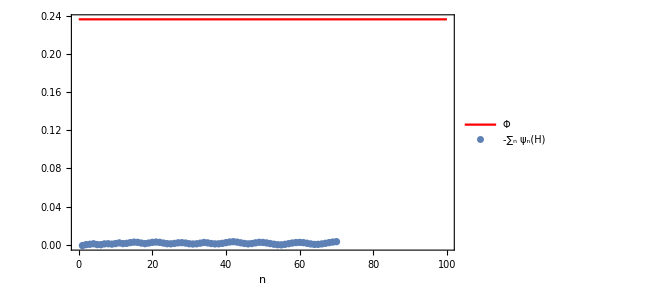

```mathematica
Show[Plot[Nu0,{x,0,Length[λτTest]},PlotStyle->Red,PlotLegends->{"Φ"}],ListPlot[-Re[Accumulate[ψHR]],Filling->Axis,PlotLegends->{"-∑_n ψ_n(H)"}],Frame->True,PlotRange->All,FrameLabel->{"n",""},ImageSize->480]
```

List of the complex conjugate eigenvalues:

```mathematica
ψHCC={};For[n=1,n<=Length[λτTest],n++,If[Im[ψH[[n]]]==0,Null,AppendTo[ψHCC,ψH[[n]]]]];ψHCC
```

{0.380812-0.37816 ⅈ,0.380812+0.37816 ⅈ,0.38873-0.629643 ⅈ,0.38873+0.629643 ⅈ,0.354485-0.937277 ⅈ,0.354485+0.937277 ⅈ,0.348486-1.2648 ⅈ,0.348486+1.2648 ⅈ,0.348066-1.58648 ⅈ,0.348066+1.58648 ⅈ,0.348313-1.9062 ⅈ,0.348313+1.9062 ⅈ,0.348613-2.22514 ⅈ,0.348613+2.22514 ⅈ,0.348865-2.5437 ⅈ,0.348865+2.5437 ⅈ,0.349064-2.86208 ⅈ,0.349064+2.86208 ⅈ,0.34922-3.18035 ⅈ,0.34922+3.18035 ⅈ,0.34934-3.49857 ⅈ,0.34934+3.49857 ⅈ,0.349437-3.81674 ⅈ,0.349437+3.81674 ⅈ,0.349514-4.13489 ⅈ,0.349514+4.13489 ⅈ,0.349578-4.45302 ⅈ,0.349578+4.45302 ⅈ,0.349629-4.77114 ⅈ,0.349629+4.77114 ⅈ}

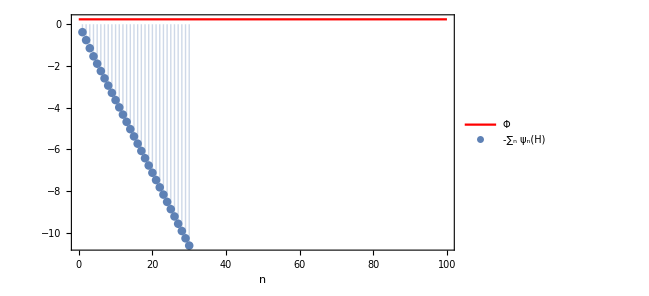

```mathematica
Show[Plot[Nu0,{x,0,Length[λτTest]},PlotStyle->Red,PlotLegends->{"Φ"}],ListPlot[-Re[Accumulate[ψHCC]],Filling->Axis,PlotLegends->{"-∑_n ψ_n(H)"}],Frame->True,PlotRange->All,FrameLabel->{"n",""},ImageSize->480]
```

Unfortunately the series does not seem to converge, showing diverging values close to the rank of the eigenvalues becoming complex conjugate as μτ crossed the bifurcation value.

```mathematica
NuTest[t_,NoM_]:=1/τ(Nu0+Re[∑_(n=1)^NoM ⅇ^(λτTest[[n]]t/τ)ψH[[n]]]);
```

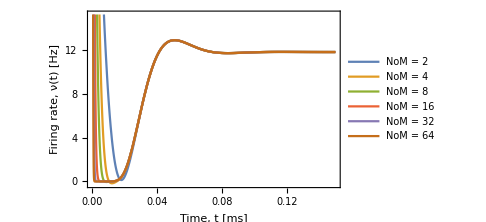

```mathematica
hgNu=Plot[{NuTest[t,2],NuTest[t,4],NuTest[t,8],NuTest[t,16],NuTest[t,32],NuTest[t,64]},{t,0,0.15},PlotRange->{-0.25,15.25},PlotLegends->{"NoM = 2","NoM = 4","NoM = 8","NoM = 16","NoM = 32","NoM = 64"},FrameLabel->{"Time, t [ms]","Firing rate, ν(t) [Hz]"},Frame->True,ImageSize->360]
```

```mathematica
Export["NuTransient.pdf",hgNu]
```

NuTransient.pdf

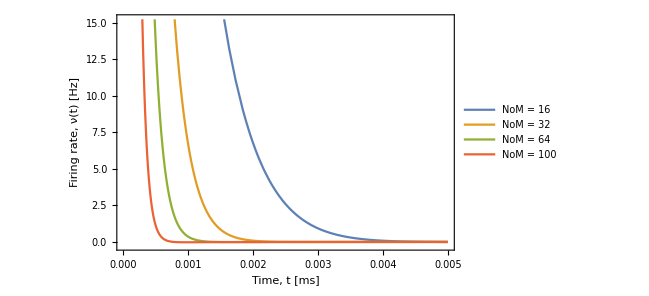

```mathematica
Plot[{NuTest[t,16],NuTest[t,32],NuTest[t,64],NuTest[t,100]},{t,0,0.005},PlotRange->{-0.25,15.25},PlotLegends->{"NoM = 16","NoM = 32","NoM = 64","NoM = 100"},PlotLegends->Automatic,FrameLabel->{"Time, t [ms]","Firing rate, ν(t) [Hz]"},Frame->True,ImageSize->480]
```

#### Convergence of the series to estimate c_v

```mathematica
t1=-NLimit[D[ρISI[s,XrTest,XtTest], s],s->0];
t2=NLimit[D[ρISI[s,XrTest,XtTest], s,s],s->0];
Cv2fromRho=(t2-t1^2)/t1^2
```

0.348568

```mathematica
Cv2Test[NoM_]:=1-Re[2∑_(n=1)^NoM ψH[[n]]/λτTest[[n]]];
```

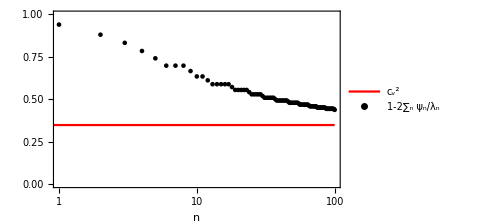

```mathematica
hgCv=Show[LogLinearPlot[Cv2fromRho,{x,0,Length[λτTest]},PlotStyle->Red,PlotLegends->{"c_v^2"},PlotRange->{{1,Length [λτTest]},{0,1}}],ListLogLinearPlot[Table[Cv2Test[n],{n,Length[λτTest]}],(*Filling->Axis,*)PlotRange->All,PlotStyle->Black,PlotLegends->{"1-2∑_n ψ_n/λ_n"},PlotRange->{{1,Length [λτTest]},All}],Frame->True,FrameLabel->{"n",""},ImageSize->360]
```

```mathematica
Export["Cv2Convergence.pdf",hgCv]
```

Cv2Convergence.pdf